```mathematica
ClearAll[f,f1,f2,g, s,x,x1,x2, W1,W2,w11,w12, w21, w22]
```

## Градиент простой функции

```mathematica
activation[x_]:=Exp[x];
f[z_,w_]:=activation[z.w]; (* экспонента от скалярного произведения x и w *)
x={x1,x2}; W1={w11,w12};
TableForm[{
"f(x,W1)="f[x,W1],
"gradient="MatrixForm[Grad[f[x,W1],W1]]
}]
```

f(x,W1)= ⅇ^(w11 x1+w12 x2)
gradient= (ⅇ^(w11 x1+w12 x2) x1
ⅇ^(w11 x1+w12 x2) x2)

## Усложним функцию активации

```mathematica
activation[x_]:=Exp[-x^2];
f[z_,w_]:=activation[z.w]; (* экспонента от минус квадарата скалярного произведения x и w *)
x={x1,x2}; W1={w11,w12};
{f[x,W1],MatrixForm[Grad[f[x,W1],W1]]}
```

{ⅇ^(-(w11 x1+w12 x2)^2),(-2 ⅇ^(-(w11 x1+w12 x2)^2) x1 (w11 x1+w12 x2)
-2 ⅇ^(-(w11 x1+w12 x2)^2) x2 (w11 x1+w12 x2))}

```mathematica
activation[x_]:=Exp[-x^2];
f[z_,w_]:=activation[z.w]; (* экспонента от минус квадарата скалярного произведения x и w *)
x={x1,x2}; W3={{w11,w12},{w21, w22}};
MatrixForm[{Grad[f[x,W3],W3[[1]]],Grad[f[x,W3],W3[[2]]]}]
```

((-2 ⅇ^(-(w11 x1+w21 x2)^2) x1 (w11 x1+w21 x2)
0) | (0
-2 ⅇ^(-(w12 x1+w22 x2)^2) x1 (w12 x1+w22 x2))
(-2 ⅇ^(-(w11 x1+w21 x2)^2) x2 (w11 x1+w21 x2)
0) | (0
-2 ⅇ^(-(w12 x1+w22 x2)^2) x2 (w12 x1+w22 x2)))

## Градиент сложной функции

```mathematica
f2[x_, w1_, w2_]:=f[f[x,w1], w2];
W2={w21,w22};
MatrixForm[Grad[f2[x,W1,W2],Join[W1, W2]]]
```

(-2 ⅇ^(-(ⅇ^(-(w11 x1+w12 x2)^2).{w21,w22})^2) ⅇ^(-(w11 x1+w12 x2)^2).{w21,w22} (ⅇ^(-(w11 x1+w12 x2)^2).{{0,0,1,0},{0,0,0,1}}+(-2 ⅇ^(-(w11 x1+w12 x2)^2) x1 (w11 x1+w12 x2)).{w21,w22})
-2 ⅇ^(-(ⅇ^(-(w11 x1+w12 x2)^2).{w21,w22})^2) ⅇ^(-(w11 x1+w12 x2)^2).{w21,w22} (ⅇ^(-(w11 x1+w12 x2)^2).{{0,0,1,0},{0,0,0,1}}+(-2 ⅇ^(-(w11 x1+w12 x2)^2) x2 (w11 x1+w12 x2)).{w21,w22})
-2 ⅇ^(-(ⅇ^(-(w11 x1+w12 x2)^2).{w21,w22})^2) ⅇ^(-(w11 x1+w12 x2)^2).{w21,w22} ⅇ^(-(w11 x1+w12 x2)^2).{{0,0,1,0},{0,0,0,1}}
-2 ⅇ^(-(ⅇ^(-(w11 x1+w12 x2)^2).{w21,w22})^2) ⅇ^(-(w11 x1+w12 x2)^2).{w21,w22} ⅇ^(-(w11 x1+w12 x2)^2).{{0,0,1,0},{0,0,0,1}})

## Графики производных

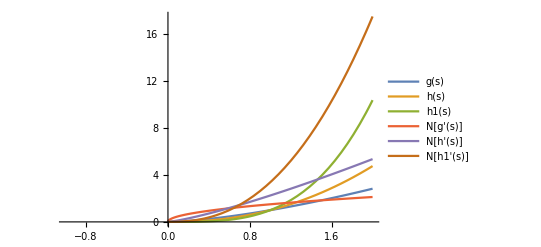

```mathematica
g[s_]:=s^1.5;
(*g[s_]:=Exp[-s^2/4];*)
(*g[s_]:=Tanh[s];*)
h[s_]:=g[g[s]];
h1[s_]:=g[g[g[s]]];
Plot[{g[s],h[s],h1[s],N[g'[s]],N[h'[s]],N[h1'[s]]},{s,-1,2},PlotLegends->"Expressions", PlotRange->Full]
```

## Проблема “взрыва” градиента степенных функций

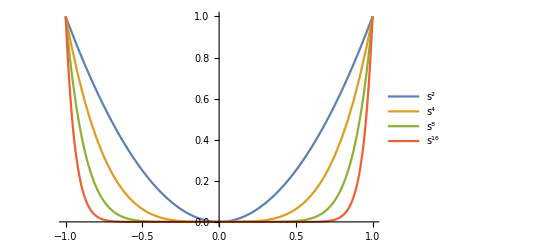
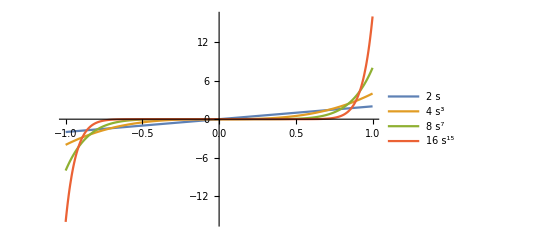

```mathematica
g[s_]:=s^2;
t=RecurrenceTable[{a[n+1]==g[a[n]], a[1]==g[s]},a,{n,1,4}];
dt=D[t,s]; 
TableForm[{Plot[t,{s,-1,1},PlotLegends->"Expressions", PlotRange->Full],Plot[dt,{s,-1,1},PlotLegends->"Expressions", PlotRange->Full]}]
```

## Проблема “угасания” градиента негативно-степенных функций

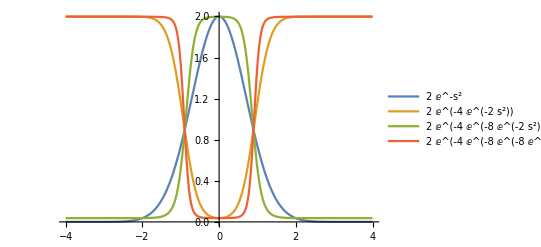
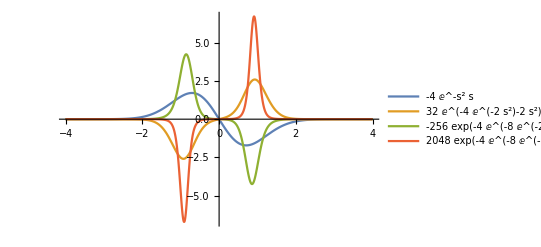

```mathematica
g[s_]:=2Exp[-s^2]; (* 1/(2*Exp[s^2])  *)
t=RecurrenceTable[{a[n+1]==g[a[n]], a[1]==g[s]},a,{n,1,4}];
dt=D[t,s]; 
TableForm[{Plot[t,{s,-4,4},PlotLegends->"Expressions", PlotRange->Full],Plot[dt,{s,-4,4},PlotLegends->"Expressions", PlotRange->Full]}]
```

## Решение проблем “взрыва”/”угасания”- специальные функции

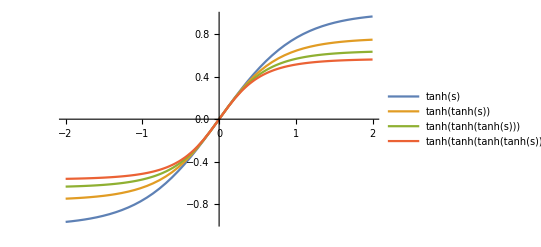
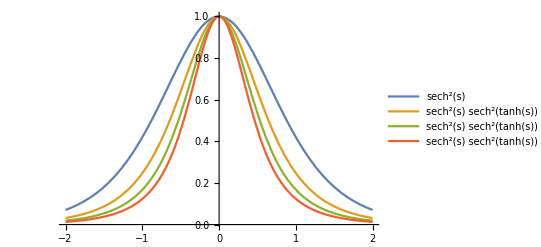

```mathematica
g[s_]:=Tanh[s];
t=RecurrenceTable[{a[n+1]==g[a[n]], a[1]==g[s]},a,{n,1,4}];
dt=D[t,s]; 
TableForm[{Plot[t,{s,-2,2},PlotLegends->"Expressions", PlotRange->Full],Plot[dt,{s,-2,2},PlotLegends->"Expressions", PlotRange->Full]}]
```

## Проблема локальных минимумов

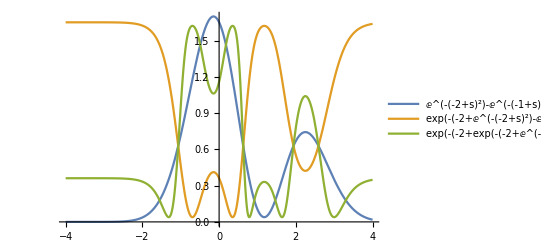
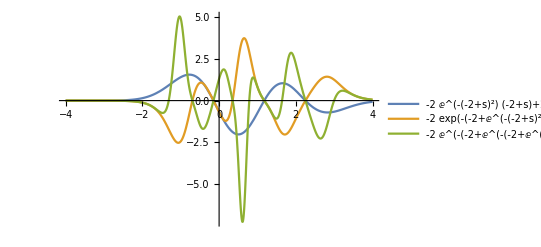

```mathematica
g[s_]:=2Exp[-s^2]-Exp[-(s-1)^2]+Exp[-(s-2)^2];
t=RecurrenceTable[{a[n+1]==g[a[n]], a[1]==g[s]},a,{n,1,3}];
dt=D[t,s]; 
TableForm[{Plot[t,{s,-4,4},PlotLegends->"Expressions", PlotRange->Full],Plot[dt,{s,-4,4},PlotLegends->"Expressions", PlotRange->Full]}]
```

```mathematica
N[13470/50]
```

269.4